```mathematica
IntermediateFunction[x_,a_,c_]:=a*π*(ProductLog[2*x])^c
IntermediateFunctionAlt[x_,a_,c_]:=a*π*(ProductLog[2*x])^2 Exp[-c*x]
```

## σ_T

```mathematica
σTsmall[β_]:=2 π β^2(1/2+β^2(-BesselK[1, β]^2+BesselK[0,β]BesselK[2,β]))
```

### Attractive

```mathematica
γ[β_]:=Sqrt[π/β] Erfi[Sqrt[ProductLog[2β]/2]]-1/ProductLog[2β]
```

```mathematica
σTlargeatt[β_]:=π((1+Log[β]-1/(2 Log[β]))^2-1/γ[β]^2)
```

```mathematica
βlow=0.2;
βhigh=50;
```

```mathematica
sol=FindRoot[{σTsmall[βlow]==IntermediateFunctionAlt[βlow,a,c],σTlargeatt[βhigh]==IntermediateFunctionAlt[βhigh,a,c]},{{a,2},{c,0.01}}]
```

{a→2.77743,c→0.0115272}

```mathematica
σT[β_]:=Piecewise[{{σTsmall[β],β≤βlow},{IntermediateFunctionAlt[β,a,c]/.sol,β>βlow&&β<βhigh},{σTlargeatt[β],β≥βhigh}}]
```

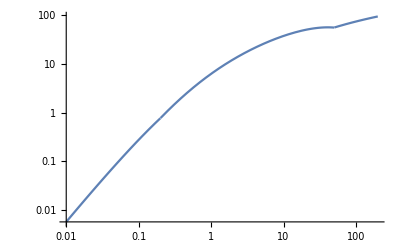

```mathematica
P1=LogLogPlot[{σT[β]},{β,0.01,200}]
```

### Repulsive

```mathematica
σTlargerep[β_]:=π*1.20*ProductLog[2β]^2
```

```mathematica
βlow=0.2;
βhigh=10;
```

```mathematica
sol=FindRoot[{σTsmall[βlow]==IntermediateFunction[βlow,a,c],σTlargerep[βhigh]==IntermediateFunction[βhigh,a,c]},{{a,5},{c,0.1}}]
```

{a→1.66948,c→1.58242}

```mathematica
σT[β_]:=Piecewise[{{σTsmall[β],β≤βlow},{IntermediateFunction[β,a,c]/.sol,β>βlow&&β<βhigh},{σTlargerep[β],β≥βhigh}}]
```

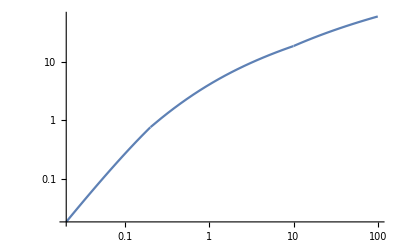

```mathematica
LogLogPlot[σT[β],{β,0.1*βlow,10*βhigh}]
```

## σ_V

```mathematica
σVsmall[β_]:=4 π β^2(1/2+4β^2(-BesselK[1,2 β]^2+BesselK[0,2β]BesselK[2,2β]))
```

### Attractive

```mathematica
σVlargeatt[β_]:=π/2(1+Log[β]-1/(2 Log[β]))^2
```

```mathematica
βlow=0.2;
βhigh=20;
```

```mathematica
sol=FindRoot[{σVsmall[βlow]==IntermediateFunction[βlow,a,c],σVlargeatt[βhigh]==IntermediateFunction[βhigh,a,c]},{{a,5},{c,1}}]
```

{a→1.74421,c→1.44714}

```mathematica
σV[β_]:=Piecewise[{{σVsmall[β],β≤βlow},{IntermediateFunction[β,a,c]/.sol,β>βlow&&β<βhigh},{σVlargeatt[β],β≥βhigh}}]
```

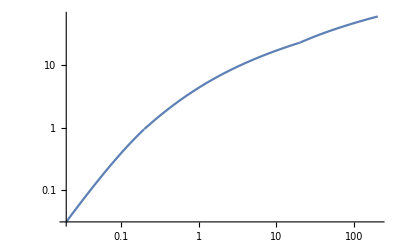

```mathematica
LogLogPlot[σV[β],{β,0.1*βlow,10*βhigh}]
```

### Repulsive

```mathematica
σVlargerep[β_]:=0.793 π ProductLog[2β]^2+π/2(ProductLog[4π β^2]^2/4-ProductLog[2β]^2)
```

```mathematica
βlow=0.2;
βhigh=5;
```

```mathematica
sol=FindRoot[{σVsmall[βlow]==IntermediateFunction[βlow,a,c],σVlargerep[βhigh]==IntermediateFunction[βhigh,a,c]},{{a,5},{c,10}}]
```

{a→1.52035,c→1.33394}

```mathematica
σV[β_]:=Piecewise[{{σVsmall[β],β≤βlow},{IntermediateFunction[β,a,c]/.sol,β>βlow&&β<βhigh},{σVlargerep[β],β≥βhigh}}]
```

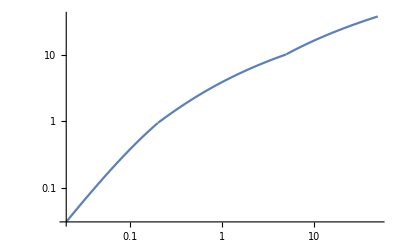

```mathematica
LogLogPlot[{σV[β]},{β,0.1*βlow,10*βhigh}]
```